```mathematica
allGraphs5[lambdaKey,"colotree"]/.RepGraph["T"]
```

--Graphics-390141+-Graphics-258682--Graphics-214203+-Graphics-199365

```mathematica
ShowGraph5Least[Bases["F","AtomKeys"][[1]]]
```

-Graphics-034

```mathematica
ShowGraph5Least[Bases["T","AtomKeys"][[1]]]
```

-Graphics-199365

```mathematica
Table[k->ShowGraph5Least[Bases["C","AtomKeys"][[k]]],{k,52}]
```

{1→-Graphics-295240,2→-Graphics-295250,3→-Graphics-295330,4→-Graphics-295270,5→-Graphics-297670,6→-Graphics-296050,7→-Graphics-295510,8→-Graphics-492070,9→-Graphics-360850,10→-Graphics-317110,11→-Graphics-302530,12→-Graphics-297681,13→-Graphics-296080,14→-Graphics-295600,15→-Graphics-492081,16→-Graphics-492161,17→-Graphics-492100,18→-Graphics-360860,19→-Graphics-361660,20→-Graphics-361120,21→-Graphics-317140,22→-Graphics-319540,23→-Graphics-317380,24→-Graphics-302621,25→-Graphics-304961,26→-Graphics-303340,27→-Graphics-295371,28→-Graphics-298571,29→-Graphics-297970,30→-Graphics-296330,31→-Graphics-560111,32→-Graphics-514750,33→-Graphics-499631,34→-Graphics-382810,35→-Graphics-368170,36→-Graphics-324411,37→-Graphics-492201,38→-Graphics-560121,39→-Graphics-514780,40→-Graphics-499721,41→-Graphics-361940,42→-Graphics-383080,43→-Graphics-368980,44→-Graphics-319840,45→-Graphics-326841,46→-Graphics-305861,47→-Graphics-298881,48→-Graphics-582881,49→-Graphics-567701,50→-Graphics-522321,51→-Graphics-390141,52→-Graphics-590481}

```mathematica
CreateKeys[base1_,base2_,keys_,prefix_]:=Block[{result,result2={}},
result=Bases[base1,"AtomKeys"];
result2=Map[ChangeSymbol[#,prefix]&,Bases[base1,"Variables"]];
Table[
result[[key]]=Bases[base2,"AtomKeys"][[key]];
result2[[key]]=ChangeSymbol[Bases[base2,"Variables"][[key]],prefix]
,{key,keys}
];
{result,result2}
]
```

```mathematica
$HistoryLength=5
```

5

## Now go for a new base

```mathematica
Select[Range[52],MemberQ[Join[quads],Bases["C","AtomKeys"][[#]]]&]
```

{4,6,7,9,10}

```mathematica
{allFunKeys,allFunVariables}=CreateKeys["C","E",Select[Range[52],!MemberQ[Join[alfa1s,quads],Bases["C","AtomKeys"][[#]]]&],"g"]
```

{{0,2,18,29527,486,29605,29551,39366,36085,31711,1458,488,29608,72,39368,39384,39372,13124,36166,36112,31714,4860,31738,1476,1944,1620,26,666,546,218,52974,43902,40878,17514,14586,5834,39392,52976,43908,40896,13340,17568,14748,4920,6320,2124,728,57528,54492,45416,18980,59048},{g1x2x3x4x5,g1x2x3x45,g1x2x34x5,g1x2x35x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x45,g1x24x35,g1x25x34,g12x3x45,g12x34x5,g12x35x4,g13x2x45,g13x24x5,g13x25x4,g14x2x35,g14x23x5,g14x25x3,g15x2x34,g15x23x4,g15x24x3,g1x2x345,g1x234x5,g1x235x4,g1x245x3,g123x4x5,g124x3x5,g125x3x4,g134x2x5,g135x2x4,g145x2x3,g12x345,g123x45,g124x35,g125x34,g13x245,g134x25,g135x24,g14x235,g145x23,g15x234,g1x2345,g1234x5,g1235x4,g1245x3,g1345x2,g12345}}

```mathematica
Table[k->ShowGraph5Least[allFunKeys[[k]]],{k,52}]
```

{1→-Graphics-034,2→-Graphics-213,3→-Graphics-1813,4→-Graphics-295270,5→-Graphics-48613,6→-Graphics-296050,7→-Graphics-295510,8→-Graphics-3936613,9→-Graphics-360850,10→-Graphics-317110,11→-Graphics-145813,12→-Graphics-4885,13→-Graphics-296080,14→-Graphics-724,15→-Graphics-393685,16→-Graphics-393845,17→-Graphics-393724,18→-Graphics-131244,19→-Graphics-361660,20→-Graphics-361120,21→-Graphics-317140,22→-Graphics-48604,23→-Graphics-317380,24→-Graphics-14765,25→-Graphics-19445,26→-Graphics-16204,27→-Graphics-265,28→-Graphics-6665,29→-Graphics-5464,30→-Graphics-2184,31→-Graphics-529745,32→-Graphics-439024,33→-Graphics-408785,34→-Graphics-175144,35→-Graphics-145864,36→-Graphics-58345,37→-Graphics-393922,38→-Graphics-529762,39→-Graphics-439081,40→-Graphics-408962,41→-Graphics-133401,42→-Graphics-175681,43→-Graphics-147481,44→-Graphics-49201,45→-Graphics-63202,46→-Graphics-21242,47→-Graphics-7282,48→-Graphics-575282,49→-Graphics-544922,50→-Graphics-454162,51→-Graphics-189802,52→-Graphics-590481}

```mathematica
Table[allGraphs5[allFunKeys[[k]],"colofun"]=allFunVariables[[k]],{k,52}]
```

{g1x2x3x4x5,g1x2x3x45,g1x2x34x5,g1x2x35x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x45,g1x24x35,g1x25x34,g12x3x45,g12x34x5,g12x35x4,g13x2x45,g13x24x5,g13x25x4,g14x2x35,g14x23x5,g14x25x3,g15x2x34,g15x23x4,g15x24x3,g1x2x345,g1x234x5,g1x235x4,g1x245x3,g123x4x5,g124x3x5,g125x3x4,g134x2x5,g135x2x4,g145x2x3,g12x345,g123x45,g124x35,g125x34,g13x245,g134x25,g135x24,g14x235,g145x23,g15x234,g1x2345,g1234x5,g1235x4,g1245x3,g1345x2,g12345}

```mathematica
repFullToFun=ToRules[
Reduce[
Table[
allGraphs5[k,"colofun"]==allGraphs5[k,"colofour"]
,
{k,allFunKeys}
],
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs5[k,"colofun"]=Simplify[allGraphs5[k,"colofour"]/.repFullToFun],
{k,Sort[Keys[allGraphs5]]}
],k];
```

```mathematica
Bases["X"]=Association[];
```

```mathematica
Bases["X","Colofour"]="colofun";
```

```mathematica
allBases=Keys[Bases]
```

{C,E,G,F,T,X}

## Working with bases

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Table[Bases[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,Bases[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,Bases[base,"Colofour"]],allGraphs5[#2,Bases[base,"Colofour"]]]&]
,{base,allBases}];
```

```mathematica
Table[Bases[base,"Variables"]=Table[allGraphs5[k,Bases[base,"Colofour"]],{k,Bases[base,"AtomKeys"]}]
,{base,allBases}];
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs5[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

239

```mathematica
Clear[RepGraph];RepGraph[base_]:=RepGraph[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ShowGraph5Least[key],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey];RepKey[base_]:=RepKey[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->key,{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial];RepChromial[base_]:=RepChromial[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[allGraphs5[key,"graph"],x],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase];RepBase[base_,base2_]:=RepBase[base,base2]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,Bases[base2,"Colofour"]],{key,Bases[base,"AtomKeys"]}]
```

## Some conversion

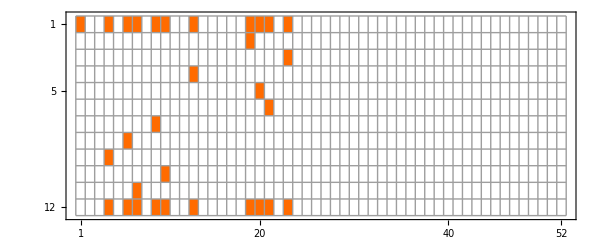
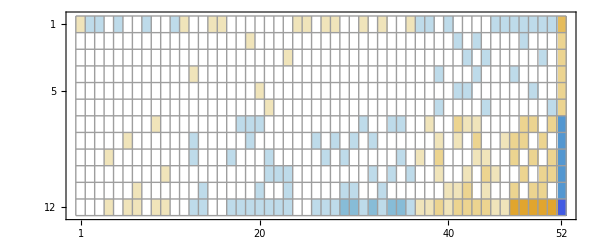
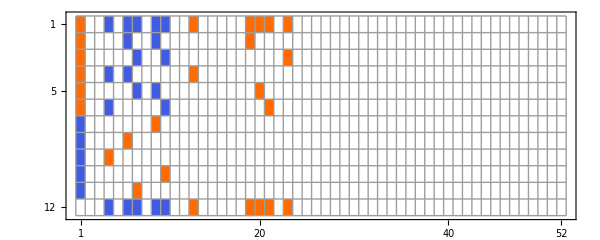
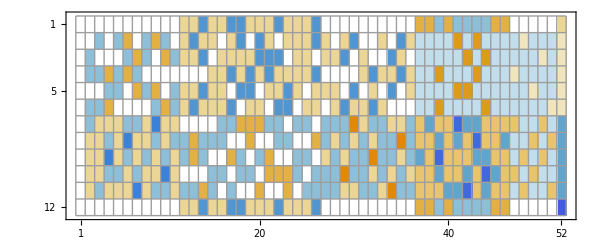
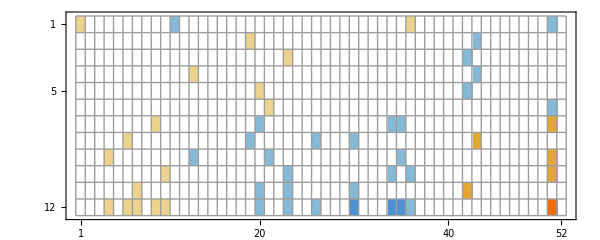
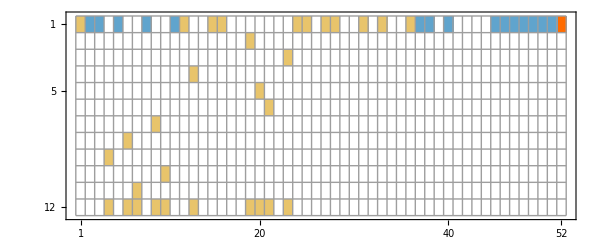
{-Graphics-C,-Graphics-E,-Graphics-G,-Graphics-F,-Graphics-T,-Graphics-X}

```mathematica
Table[
Labeled[MatrixPlot[Append[Table[BaseCoeff[k,base],{k,Prepend[Join[alfa1s,quads],lambdaKey]}],Total[Table[BaseCoeff[k,base],{k,Join[alfa1s,quads]}]]],ImageSize->600,Mesh->All],base],
{base,allBases}]
```

```mathematica
BaseFormula[lambdaKey,"C"]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
BaseFormula[lambdaKey,"X"]/.RepGraph["X"]
```

4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-454162--Graphics-408962--Graphics-393922--Graphics-189802--Graphics-63202--Graphics-21242--Graphics-7282+-Graphics-529745+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-6665+-Graphics-19445+-Graphics-4885+-Graphics-58345+-Graphics-14765+-Graphics-265--Graphics-3936613--Graphics-48613--Graphics-1813--Graphics-145813--Graphics-213+-Graphics-034

```mathematica
Table[
Labeled[MatrixForm[Append[Table[BaseCoeff[k,base],{k,Prepend[Join[alfa1s,quads],lambdaKey]}],Total[Table[BaseCoeff[k,base],{k,Join[alfa1s,quads]}]]],TableSpacing->{0, 0},TableHeadings->{None, Table[Rotate[SymbolToLabel2[v],Pi/2],{v,Bases[base,"Variables"]}]}],base],
{base,allBases}]
```

{(OverHat[1] | 45 | 34 | 35 | 23 | 24 | 25 | 12 | 13 | 14 | 15 | 23♁45 | 24♁35 | 25♁34 | 12♁45 | 12♁34 | 12♁35 | 13♁45 | 13♁24 | 13♁25 | 14♁35 | 14♁23 | 14♁25 | 15♁34 | 15♁23 | 15♁24 | 345 | 234 | 235 | 245 | 123 | 124 | 125 | 134 | 135 | 145 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 2345 | 1234 | 1235 | 1245 | 1345 | OverHat[0]
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)C,(OverHat[1] | 45 | 34 | 35 | 23 | 24 | 25 | 12 | 13 | 14 | 15 | 23♁45 | 24♁35 | 25♁34 | 12♁45 | 12♁34 | 12♁35 | 13♁45 | 13♁24 | 13♁25 | 14♁35 | 14♁23 | 14♁25 | 15♁34 | 15♁23 | 15♁24 | 345 | 234 | 235 | 245 | 123 | 124 | 125 | 134 | 135 | 145 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 2345 | 1234 | 1235 | 1245 | 1345 | OverHat[0]
1 | -1 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 2 | -6
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 0 | 1 | 2 | 2 | 0 | 2 | 0 | -6
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 2 | 0 | 2 | 0 | 2 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 1 | 0 | 0 | 2 | 0 | 2 | 2 | -6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 1 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | -6
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -2 | -2 | -1 | -2 | -1 | -2 | -2 | -1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 5 | 5 | 5 | 5 | 5 | -20)E,(OverHat[1] | 45 | 34 | 35 | 23 | 24 | 25 | 12 | 13 | 14 | 15 | 23♁45 | 24♁35 | 25♁34 | 12♁45 | 12♁34 | 12♁35 | 13♁45 | 13♁24 | 13♁25 | 14♁35 | 14♁23 | 14♁25 | 15♁34 | 15♁23 | 15♁24 | 345 | 234 | 235 | 245 | 123 | 124 | 125 | 134 | 135 | 145 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 2345 | 1234 | 1235 | 1245 | 1345 | OverHat[0]
1 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)G,(OverHat[1] | 45 | 34 | 35 | 23 | 24 | 25 | 12 | 13 | 14 | 15 | 23♁45 | 24♁35 | 25♁34 | 12♁45 | 12♁34 | 12♁35 | 13♁45 | 13♁24 | 13♁25 | 14♁35 | 14♁23 | 14♁25 | 15♁34 | 15♁23 | 15♁24 | 345 | 234 | 235 | 245 | 123 | 124 | 125 | 134 | 135 | 145 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 2345 | 1234 | 1235 | 1245 | 1345 | OverHat[0]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | 1/6
0 | 0 | -1/6 | 0 | -1/6 | 1/3 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 0 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | -1/3 | 0 | 0 | 1/6 | 0 | -1/3 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | -1/6 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 0 | 1/3 | -1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 0 | 0 | -1/3 | 1/6 | 0 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | 1/12
0 | -1/6 | -1/6 | 1/3 | -1/6 | 1/3 | -1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12
0 | 0 | 0 | -1/6 | -1/6 | 0 | 1/3 | -1/6 | 1/3 | 0 | -1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 1/6 | 1/6 | 1/6 | 0 | -1/3 | 0 | 1/6 | 0 | -1/3 | 0 | 1/6 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | -1/12 | -1/12 | 1/12
0 | -1/6 | -1/6 | 1/3 | 0 | 0 | 0 | 0 | -1/6 | 1/3 | -1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 1/6 | 1/6 | 0 | -1/3 | -1/3 | 0 | 1/6 | 1/6 | 0 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | 1/6 | 0 | 0 | 0 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | 5/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | -1/12 | 1/12 | 1/12
0 | -1/6 | 1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | -1/6 | -1/6 | 1/3 | 1/3 | 1/3 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/2 | 1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | 1/4 | -1/4 | 1/4 | 1/4 | -3/4 | -1/4 | -1/4 | 1/4 | 1/4 | 1/4 | 1/4 | -1/12 | -1/12 | 1/4 | -1/12 | -1/4
0 | 1/6 | 1/6 | -1/6 | 1/6 | -1/2 | 1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 0 | 1/3 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | 1/4 | 1/4 | -1/4 | 1/4 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | -1/4 | -1/12 | -1/12 | 1/4 | -1/12 | 1/4 | -1/4
0 | 1/6 | 1/6 | -1/2 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/3 | -1/6 | 0 | 0 | 1/3 | -1/6 | 0 | -1/6 | 1/3 | 0 | 0 | -1/6 | -1/6 | 0 | 1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | -1/4 | 1/4 | -3/4 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | 1/4 | -1/12 | -1/4
0 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/6 | -1/2 | 1/6 | 0 | 0 | 0 | -1/6 | -1/6 | 0 | -1/6 | -1/6 | 0 | 1/3 | 1/3 | 1/3 | -1/6 | 0 | -1/6 | -1/6 | -1/6 | 1/2 | -1/6 | -1/6 | 1/6 | -1/6 | 1/6 | -1/6 | 1/6 | 1/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/4 | 1/4 | -3/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | -1/4
0 | 1/6 | -1/6 | 1/6 | 1/6 | 1/6 | -1/2 | 1/6 | -1/6 | -1/6 | 1/6 | -1/6 | -1/6 | 1/3 | -1/6 | 0 | -1/6 | 0 | 0 | 1/3 | 0 | 0 | 1/3 | 0 | -1/6 | -1/6 | -1/6 | -1/6 | 1/6 | 1/6 | -1/6 | -1/6 | 1/6 | 1/2 | -1/6 | -1/6 | 1/4 | 1/4 | 1/4 | -1/4 | -1/4 | -3/4 | 1/4 | -1/4 | 1/4 | 1/4 | -1/12 | 1/4 | -1/12 | -1/12 | 1/4 | -1/4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | -1/3 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 1/6 | 1/6 | 1/6 | -1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/3 | 1/3 | -1/6 | 1/3 | -1/6 | -1/6 | -1/6 | -1/6 | 1/3 | 1/3 | 0 | 0 | 0 | 0 | 0 | -5/6)F,(OverHat[1] | 45 | 34 | 35 | 23 | 24 | 25 | 12 | 13 | 14 | 15 | 23♁45 | 24♁35 | 25♁34 | 12♁45 | 12♁34 | 12♁35 | 13♁45 | 13♁24 | 13♁25 | 14♁35 | 14♁23 | 14♁25 | 15♁34 | 15♁23 | 15♁24 | 345 | 234 | 235 | 245 | 123 | 124 | 125 | 134 | 135 | 145 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 2345 | 1234 | 1235 | 1245 | 1345 | OverHat[0]
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | -2 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 0)T,(OverHat[1] | 45 | 34 | 35 | 23 | 24 | 25 | 12 | 13 | 14 | 15 | 23♁45 | 24♁35 | 25♁34 | 12♁45 | 12♁34 | 12♁35 | 13♁45 | 13♁24 | 13♁25 | 14♁35 | 14♁23 | 14♁25 | 15♁34 | 15♁23 | 15♁24 | 345 | 234 | 235 | 245 | 123 | 124 | 125 | 134 | 135 | 145 | 12♁345 | 123♁45 | 124♁35 | 125♁34 | 13♁245 | 134♁25 | 135♁24 | 14♁235 | 145♁23 | 15♁234 | 2345 | 1234 | 1235 | 1245 | 1345 | OverHat[0]
1 | -1 | -1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)X}

```mathematica
.
```

```mathematica
TableForm[Table[MatrixRank[ConversionMatrix[base1,base2]],{base1,allBases},{base2,allBases}],TableHeadings->{allBases, allBases},TableAlignments->{Center, Center}]
```

| C | E | G | F | T | X
C | 52 | 52 | 52 | 52 | 52 | 52
E | 52 | 52 | 52 | 52 | 52 | 52
G | 52 | 52 | 52 | 52 | 52 | 52
F | 52 | 52 | 52 | 52 | 52 | 52
T | 52 | 52 | 52 | 52 | 52 | 52
X | 52 | 52 | 52 | 52 | 52 | 52

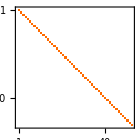
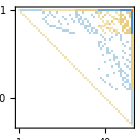
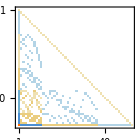
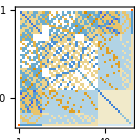
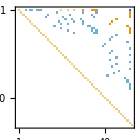
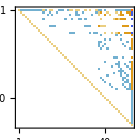
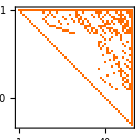
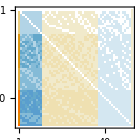
| C | E | G | F | T | X
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
X | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[base1,base2],ImageSize->140],{base1,allBases},{base2,allBases}],TableHeadings->{allBases, allBases},TableAlignments->{Center, Center}]
```

```mathematica
allGraphs5[alfa1Key,"colofun"]/.RepGraph["X"]
```

-Graphics-361660

```mathematica
allGraphs5[alfa1Key,"colofourrealnull"]/.RepGraph["E"]
```

2 -Graphics-590481--Graphics-575282--Graphics-147481--Graphics-133401+-Graphics-132842

```mathematica
allGraphs5[quad1Key,"colofourrealnull"]/.RepGraph["E"]
```

-6 -Graphics-590481+2 -Graphics-575282+2 -Graphics-544922+-Graphics-529762+2 -Graphics-189802+-Graphics-147481+2 -Graphics-133401+-Graphics-175681--Graphics-529745--Graphics-175144--Graphics-132842--Graphics-145864--Graphics-131762--Graphics-131244+-Graphics-1312210

```mathematica
allGraphs5[quad1Key,"colofun"]/.RepGraph["X"]
```

-Graphics-360850

```mathematica
Table[
Table[Framed[Labeled[ShowGraph5Least[k],base]]->(Expand[BaseFormula[k,base]]/.RepGraph[base]),{base,allBases}],
 {k,{alfa1Key,quad1Key,lambdaKey}}]
```

{{-Graphics-361660C→-Graphics-361660,-Graphics-361660E→2 -Graphics-590481--Graphics-575282--Graphics-147481--Graphics-133401+-Graphics-132842,-Graphics-361660G→-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240,-Graphics-361660F→-(-Graphics-1968321)/6+(-Graphics-656124)/3-(-Graphics-218724)/6-(-Graphics-24321)/6+(-Graphics-8124)/3-(-Graphics-921)/6+(-Graphics-1968615)/6+(-Graphics-1968413)/6-(-Graphics-658816)/3-(-Graphics-656215)/3+(-Graphics-221416)/6+(-Graphics-219016)/6+(-Graphics-97213)/6-(-Graphics-81015)/3+(-Graphics-73813)/6+(-Graphics-24413)/6-(-Graphics-8416)/3+(-Graphics-3615)/6+(-Graphics-204398)/6-(-Graphics-72939)/3+(-Graphics-29178)/6+(-Graphics-2739)/6-(-Graphics-1099)/3+(-Graphics-138)/6-(-Graphics-264885)/12-(-Graphics-219545)/12-(-Graphics-204485)/12-(-Graphics-196965)/12-(-Graphics-87845)/12+(5 -Graphics-73745)/12+(5 -Graphics-66705)/12-(-Graphics-31605)/12-(-Graphics-24605)/12-(-Graphics-10625)/12+(-Graphics-287640)/12-(-Graphics-272460)/12-(-Graphics-227080)/12-(-Graphics-94900)/12-(-Graphics-3640)/12+(-Graphics-295240)/12,-Graphics-361660T→--Graphics-368980+-Graphics-354340,-Graphics-361660X→-Graphics-361660},{-Graphics-360850C→-Graphics-360850,-Graphics-360850E→-6 -Graphics-590481+2 -Graphics-575282+2 -Graphics-544922+-Graphics-529762+2 -Graphics-189802+-Graphics-147481+2 -Graphics-133401+-Graphics-175681--Graphics-529745--Graphics-175144--Graphics-132842--Graphics-145864--Graphics-131762--Graphics-131244+-Graphics-1312210,-Graphics-360850G→-Graphics-229630--Graphics-295240,-Graphics-360850F→(-Graphics-1968321)/6-(-Graphics-656124)/2+(-Graphics-218724)/6+(-Graphics-72921)/6+(-Graphics-24321)/6-(-Graphics-8124)/6-(-Graphics-2724)/6+(-Graphics-921)/6+(-Graphics-324)/6-(-Graphics-121)/6-(-Graphics-1969213)/6-(-Graphics-1968615)/6+(-Graphics-664216)/3+(-Graphics-658816)/3+(-Graphics-656215)/3-(-Graphics-243015)/6-(-Graphics-219016)/6-(-Graphics-97213)/6-(-Graphics-73813)/6+(-Graphics-264878)/6-(-Graphics-219519)/6-(-Graphics-204398)/6+(-Graphics-87579)/6+(-Graphics-72939)/6-(-Graphics-29178)/6-(-Graphics-3338)/6-(-Graphics-2739)/6+(-Graphics-1099)/2-(-Graphics-138)/6-(-Graphics-264885)/4+(-Graphics-219545)/4+(-Graphics-204485)/4+(-Graphics-196965)/4-(-Graphics-87845)/4-(-Graphics-73745)/4-(3 -Graphics-66705)/4+(-Graphics-31605)/4+(-Graphics-24605)/4+(-Graphics-10625)/4-(-Graphics-287640)/12-(-Graphics-272460)/12+(-Graphics-227080)/4-(-Graphics-94900)/12+(-Graphics-3640)/4-(-Graphics-295240)/4,-Graphics-360850T→2 -Graphics-390141--Graphics-375481--Graphics-346201--Graphics-339160+-Graphics-331301,-Graphics-360850X→-Graphics-360850},{-Graphics-206653C→-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240,-Graphics-206653E→4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-454162--Graphics-408962--Graphics-393922--Graphics-189802--Graphics-63202--Graphics-21242--Graphics-7282+-Graphics-529745+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-6665+-Graphics-19445+-Graphics-4885+-Graphics-58345+-Graphics-14765+-Graphics-265--Graphics-3936613--Graphics-48613--Graphics-1813--Graphics-145813--Graphics-213+-Graphics-034,-Graphics-206653G→-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240,-Graphics-206653F→(-Graphics-1969213)/6-(-Graphics-1968615)/3+(-Graphics-1968413)/6+(-Graphics-664216)/6+(-Graphics-658816)/6-(-Graphics-656215)/3-(-Graphics-243015)/3+(-Graphics-221416)/6+(-Graphics-219016)/6+(-Graphics-97213)/6-(-Graphics-81015)/3+(-Graphics-73813)/6+(-Graphics-24413)/6+(-Graphics-8416)/6-(-Graphics-3615)/3+(-Graphics-264885)/3-(-Graphics-219545)/6+(-Graphics-204485)/3+(-Graphics-196965)/3-(-Graphics-87845)/6-(-Graphics-73745)/6-(-Graphics-66705)/6+(-Graphics-31605)/3-(-Graphics-24605)/6+(-Graphics-10625)/3+(-Graphics-295240)/6,-Graphics-206653T→--Graphics-390141+-Graphics-258682--Graphics-214203+-Graphics-199365,-Graphics-206653X→4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-454162--Graphics-408962--Graphics-393922--Graphics-189802--Graphics-63202--Graphics-21242--Graphics-7282+-Graphics-529745+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-6665+-Graphics-19445+-Graphics-4885+-Graphics-58345+-Graphics-14765+-Graphics-265--Graphics-3936613--Graphics-48613--Graphics-1813--Graphics-145813--Graphics-213+-Graphics-034}}

```mathematica
(allGraphs5[19683,"embed"]*24)/23
```

9312/23

```mathematica
With[{base="X"},
Simplify[Total[Table[BaseFormula[k,base],{k,alfa1s}]]==0]/.RepGraph["X"]
]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080==0

```mathematica
ConversionMatrix["C","F"]//Flatten//Tally//Sort
```

{{-3/4,20},{-1/2,10},{-11/24,10},{-1/3,120},{-1/4,80},{-1/6,280},{-1/8,5},{-1/12,660},{-1/24,30},{0,446},{1/24,211},{1/12,120},{1/6,390},{1/4,160},{1/3,60},{5/12,80},{1/2,20},{1,2}}